```mathematica
Clear["Global`*"];
Off[General::spell];
Off[General::spell1];
```

### 3a

```mathematica
V0=3;
L=10;
```

```mathematica
V[x_]:=-V0*(Sech[x])^2/;Abs[x]≤L/2
V[x_]:=0/;Abs[x]>L/2
```

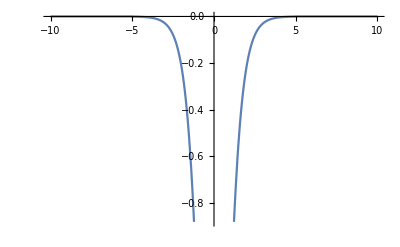

```mathematica
Plot[V[x],{x,-L,L}]
```

### 3b

```mathematica
B = 1;
```

```mathematica
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(
en = energy; 
NDSolve[
{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], ψ2'[-L/2] ==  ψ1'[-L/2]}, 
ψ2, 
{x, -L/2, 0} 
]
)
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A = B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, 10, -10} ]
```

-2.

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

### 3c

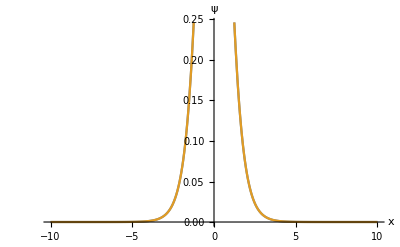

```mathematica
Plot[{ψ[x],Sqrt[3/4]*(Sech[x])^2}, 
{x, -L, L}, 
AxesLabel -> {"x", "ψ"} ]
```

### 3d

```mathematica
A = -B;
```

```mathematica
eval = en /. FindRoot [sol2[0, en] ,{en, -1, -2} ]
```

-0.5

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn [x_] := -efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[NIntegrate [ ψnn[x]^2, {x, -Infinity,Infinity} ] ];
```

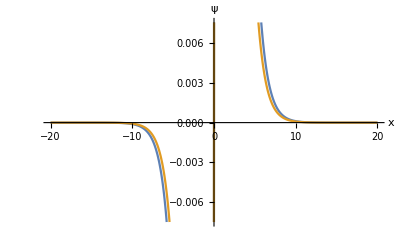

```mathematica
Plot[{ψ[x],Sqrt[3/4]*Sinh[x]*(Sech[x])^2}, 
{x, -2L,2L},
AxesLabel -> {"x", "ψ"} 
]
```

### 3e

```mathematica
V0=10;
L=10;
V[x_]:=-V0*(Sech[x])^2/;Abs[x]≤L/2
V[x_]:=0/;Abs[x]>L/2
```

```mathematica
BB={}
```

{}

```mathematica
Do[BB=Append[BB,en /. FindRoot [sol2prime[0, en] ,{en, -i, -i-1} ]], {i,1,50}]
```

```mathematica
BB=Reverse[Sort[DeleteDuplicates[BB,Abs[#1-#2]<0.001&]]]
```

{46.,-2.,-8.,-21.9139,-23.863,-26.5603,-35.3692,-47.4138,-50.9378,-59.8021}

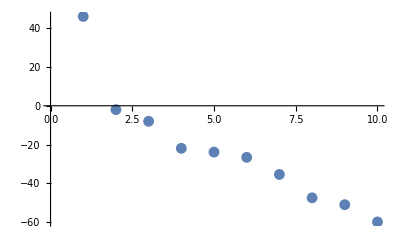

```mathematica
ListPlot[Table[{x,BB[[x]]},{x,1,Length[BB]}]]
```